```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/INI/MMB paper/figures/expression

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["expressionout.txt","CSV"];
```

```mathematica
simdata1=simdata;
```

```mathematica
simdata1[[All,1]]=simdata[[All,1]]/3600;
```

```mathematica
simdata1[[All,3]]=simdata[[All,3]]-simdata[[All,2]];
```

```mathematica
plotdata=Table[Table[{simdata1[[row,1]],simdata1[[row,col]]},{row,Length[simdata1]}],{col,2,Length[simdata1[[1]]]}];
```

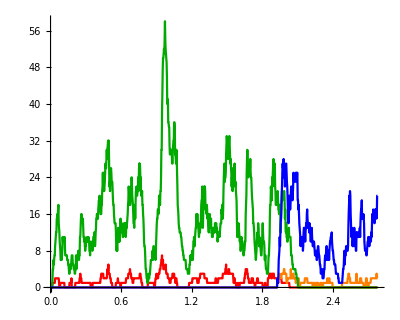

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,AspectRatio->0.8,AxesStyle->Bold,PlotStyle->{Red,Orange,Darker[Green],Blue}]
```

```mathematica
N[6809/3600]
```

1.89139